```mathematica
fixLegend[size_][legend_]:=ReplaceAll[legend,{g_Graphics:>Show[g,ImageSize->Automatic->{Automatic,size},BaselinePosition->Axis],Pane->Function@#}]
MakeBoxes[stripGridAlignment[expr_],form_]^:=ReplaceAll[MakeBoxes[expr,form],Rule[GridBoxAlignment,_]->Sequence[]]
```

## Immune blind spots

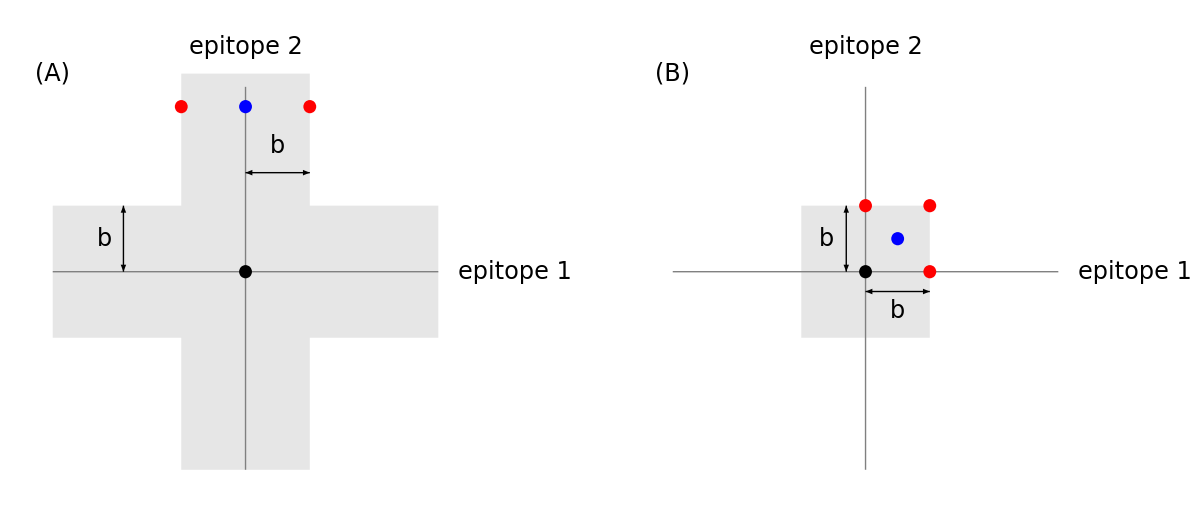

```mathematica
strainatorigin2 = Graphics[Disk[{0,0},.1]];
xaxis = Graphics[{Gray,Line[{{-3,0},{3,0}}]}];
yaxis = Graphics[{Gray,Line[{{0,2.8},{0,-3}}]}];
xaxislabel = Graphics[Text[Style["epitope 1",FontSize->24],{4.2,0}]];
yaxislabel = Graphics[Text[Style["epitope 2",FontSize->24], {0,3.4}]];
allaxes = Show[xaxis,yaxis,xaxislabel,yaxislabel];
everynbdgap1 = Graphics[{GrayLevel[0.9],Rectangle[{1,-3},{-1,3}]}];
everynbdgap2 = Graphics[{GrayLevel[0.9],Rectangle[{-3,1},{3,-1}]}];
everygappoint = Graphics[{Blue,Disk[{0,2.5},.1]}];
closeststrain1every = Graphics[{Red,Disk[{1,2.5},.1]}];
closeststrain2every = Graphics[{Red,Disk[{-1,2.5},.1]}];
everygapplot=Show[everynbdgap1, everynbdgap2,allaxes,everygappoint, strainatorigin2, closeststrain1every,closeststrain2every,
Graphics[Text[Style["b",FontSize->24],{-2.2,0.5}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{-1.9,1},{-1.9,0}}]}],
Graphics[Text[Style["b",FontSize->24],{.5,1.9}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,1.5},{1,1.5}}]}],
Graphics[Text[Style["(A)",FontSize->24],{-3,3}]],
ImagePadding->{{Automatic,Automatic},{Automatic,-100}},
ImageSize->300];

anynbdgap = Graphics[{GrayLevel[0.9],Rectangle[{-1,1},{1,-1}]}];
anygappoint = Graphics[{Blue,Disk[{.5,.5},0.1]}];
closeststrain1any = Graphics[{Red,Disk[{0,1},.1]}];
closeststrain2any = Graphics[{Red,Disk[{1,0},.1]}];
closeststrain3any = Graphics[{Red,Disk[{1,1},.1]}];
strainatoriginany = Graphics[{Black,Disk[{0,0},.1]}];
anygapplot=Show[anynbdgap,allaxes,anygappoint,strainatoriginany, closeststrain1any, closeststrain2any,closeststrain3any,
Graphics[Text[Style["b",FontSize->24],{-0.6,0.5}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{-0.3,1},{-0.3,0}}]}],
Graphics[Text[Style["b",FontSize->24],{0.5,-0.6}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,-0.3},{1,-0.3}}]}],
Graphics[Text[Style["(B)",FontSize->24],{-3,3}]],
ImageSize->300,
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}];
bothgapplots =
GraphicsRow[{everygapplot,anygapplot,
PointLegend[{Black,Red,Blue, GrayLevel[0.9]},{"strain in memory","allowed strain","immune blind spot","excluded region"},LegendMarkers->{Graphics[{Disk[{0,0},4]}],Graphics[{Disk[{0,0},4]}],Graphics[{Disk[{0,0},4]}], Graphics[{Rectangle[{-.1,-.1},{.1,.1}]}]},
LegendMarkerSize->11,LabelStyle->{FontSize->24}]}, ImageSize->1200]
```

## Any-epitope model

Wish to compute : probability of infection at the blind spot sweeping over values of b and r.
In the any-epitope model, blind spots occur in the center of a d-dimensional hypercube, and densest memory possible given a strain at the origin has strains on each lattice point with lattice constant b.

Pr(infection | densest distribution, single exposure) = product over lattice points of (1-exp(-(distance from gap point to lattice point)/r))

Coordinates of a blind spot are: (b/2, ..., b/2)
Coordinates of memory point are: (n_1 b, n_2 b, ..., n_d b)
Distance between gap point and memory point: (((n_1 - 1/2)^2 b^2 + ... + (n_d - 1/2)^2 b^2))^(1/2) = b ( ((Subscript[n, 1] - 1/2)^2 + (Subscript[n, d] - 1/2)^2))^(1/2)

We want to plot (in principle) the product over all lattice points of (1-e^(-b/r((n_1-1/2)^2+...+(n_d-1/2)^2)^(1/2)))
One potential issue is d-dependence, although note we can do this by grouping in “rings” of increasing distance from the gap point
There’s: all n_i=0, a single |n_i|=1, two |n_i|=1, one |n_i|=2, ... (partitions of s)

```mathematica
dequals2tab = Table[{rat,Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2]]),{Subscript[n, 1],-100, 100},{Subscript[n, 2],-100.,100}]},{rat, 1., 10., .5}];dequals2tab2 = Table[{rat,Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2]]),{Subscript[n, 1],-10, 10},{Subscript[n, 2],-10.,10}]},{rat, 1., 10., .5}];
```

General::munfl: Exp[-710.642] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-781.707] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-777.827] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
dequals3tab = Table[{rat,Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2+(Subscript[n, 3]-0.5)^2]]),{Subscript[n, 1],-50, 50},{Subscript[n, 2],-50.,50},{Subscript[n, 3],-50,50}]},{rat, 1., 10., .5}]
```

General::munfl: Exp[-743.483] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.608] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-733.799] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1.,1.92677×10^-12},{1.5,0.000390228},{2.,0.0405673},{2.5,0.209914},{3.,0.430344},{3.5,0.615332},{4.,0.747239},{4.5,0.835649},{5.,0.893525},{5.5,0.931087},{6.,0.955397},{6.5,0.971122},{7.,0.981296},{7.5,0.987882},{8.,0.992147},{8.5,0.99491},{9.,0.9967},{9.5,0.99786},{10.,0.998613}}

```mathematica
dequals4tab = Table[{rat,Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2+(Subscript[n, 3]-0.5)^2+(Subscript[n, 4]-0.5)^2]]),{Subscript[n, 1],-10, 10},{Subscript[n, 2],-10.,10},{Subscript[n, 3],-10,10}, {Subscript[n, 4],-10,10}]},{rat, 1., 10., .5}];
```

```mathematica
dequals4tab
```

{{1.,6.66195×10^-54},{1.5,3.50126×10^-11},{2.,0.000548293},{2.5,0.0501317},{3.,0.251238},{3.5,0.496882},{4.,0.686523},{4.5,0.81021},{5.,0.886108},{5.5,0.931737},{6.,0.959028},{6.5,0.975358},{7.,0.985151},{7.5,0.991037},{8.,0.994583},{8.5,0.996723},{9.,0.998016},{9.5,0.998798},{10.,0.999272}}

```mathematica
dequals4tab2 = Table[Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2+(Subscript[n, 3]-0.5)^2+(Subscript[n, 4]-0.5)^2]]),{Subscript[n, 1],-5, 5},{Subscript[n, 2],-5.,5},{Subscript[n, 3],-5,5}, {Subscript[n, 4],-5,5}],{rat, 1., 10., .5}];
```

```mathematica
dequals4tab3 = Table[Product[(1-Exp[-rat*Sqrt[(Subscript[n, 1]-0.5)^2+(Subscript[n, 2]-0.5)^2+(Subscript[n, 3]-0.5)^2+(Subscript[n, 4]-0.5)^2]]),{Subscript[n, 1],-2, 2},{Subscript[n, 2],-2.,2},{Subscript[n, 3],-2,2}, {Subscript[n, 4],-2,2}],{rat, 1., 10., .5}];
```

#### Note : lattice with + -2 is a good approximation (for d = 4) but + -1 is not a good approximation

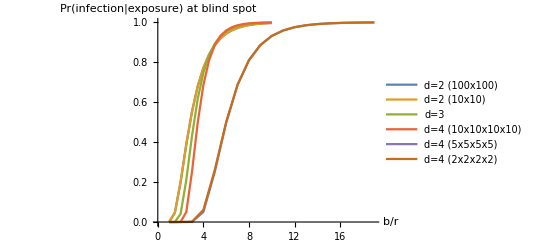

```mathematica
ListPlot[{dequals2tab,dequals2tab2, dequals3tab,dequals4tab, dequals4tab2, dequals4tab3},Joined->True, AxesLabel->{"b/r","Pr(infection|exposure) at blind spot"},PlotLegends->{"d=2 (100x100)","d=2 (10x10)","d=3","d=4 (10x10x10x10)","d=4 (5x5x5x5)","d=4 (2x2x2x2)"}]
```

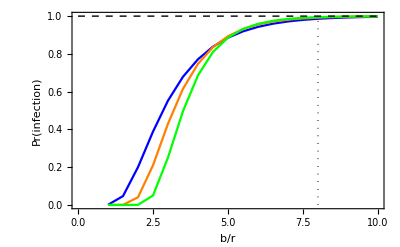

```mathematica
anyplot=Show[ListPlot[{dequals2tab, dequals3tab,dequals4tab,{{8,0},{8,1}}},Joined->True,
Frame->{True,True,False,False},
FrameStyle->{Black},
LabelStyle->{FontSize->24,Black},
PlotStyle->{Blue,Orange,Green,{Dotted,Black,Thick}},
FrameLabel->{"b/r","Pr(infection)",None,None},
ImageSize->300],
Plot[1,{x,0,10},PlotStyle->{Thick,Dashed,Black}],
ImageSize->400]
```

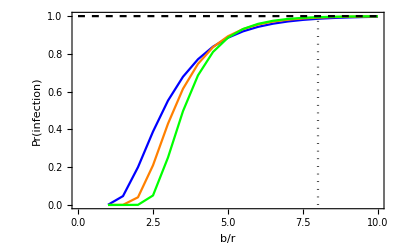
-Graphics-(D)

```mathematica
anyfig=Show[Labeled[anyplot,{Style["(D)",24,Black]},{{Top, Left}}],
ImageSize->400]
```

## Every-epitope model

Coordinates of the nearest allowed memories: Every coordinate is +-b; however at most one of these can be added.
The next-nearest memories are distance b away in the first (d-1) coordinates, and distance 2b in the dth coordinate.
After that, the first (d-1) coordinates are distance kb away and the last is kb+x, where x >> r (take x=500*r) and x>>b.
There is only one such point at each distance, no matter how many dimensions we’re in.
Gap strain: (x1, x2, ..., x_(d-1),0)

```mathematica
Clear[infterm0]
```

```mathematica
infterm0[d_,b_]:=1- E^((-(d-1)*b)/r)
```

```mathematica
infterm[d_,b_,k_]:= (1-E^(-1/r*(k^2*b^2*(d-1)+(k*b+500*r)^2)^(1/2)))
```

## Every epitope plots Collapsed as a function of b/r

```mathematica
everydequals2ctab =Table[{rat,infterm0[2,rat]*N[Product[infterm[2,rat,k],{k,0,20}]]/.{r->1}},{rat,0.1,10,.1}];
everydequals3ctab =Table[{rat,infterm0[3,rat]*N[Product[infterm[2,rat,k],{k,0,20}]]/.{r->1}},{rat,0.1,10,.1}];
everydequals4ctab =Table[{rat,infterm0[4,rat]*N[Product[infterm[2,rat,k],{k,0,20}]]/.{r->1}},{rat,0.1,10,.1}];
```

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/2.71828^710.769 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^713.224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^715.681 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

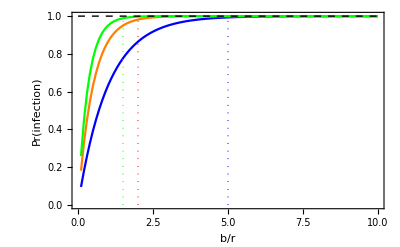

```mathematica
everyplot=
Show[ListPlot[{everydequals2ctab,everydequals3ctab,everydequals4ctab,{{5,0},{5,1}}, {{2,0},{2,1}},{{1.5,0},{1.5,1}}}, 
Joined->True,
PlotRange->All,
Frame->{True,True,False,False},
FrameStyle->{Black},
LabelStyle->{FontSize->24,Black},
FrameLabel->{"b/r","Pr(infection)",None,None},
PlotStyle->{Blue,Orange,Green,Directive[{Thick,Dotted,Blue}],Directive[{Thick,Dotted,Red}],Directive[{Thick,Dotted,Green}]},
ImageSize->300],
Plot[1,{x,0,10},PlotStyle->{Thick,Dashed, Black}] ,
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->400]
```

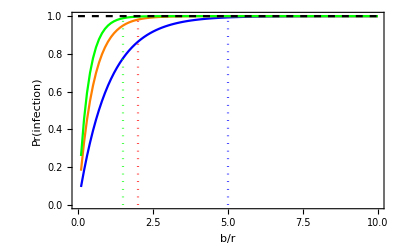
-Graphics-(C)

```mathematica
everyfig=Show[Labeled[everyplot,{Style["(C)",24,Black]},{{Top, Left}}],
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->450]
```

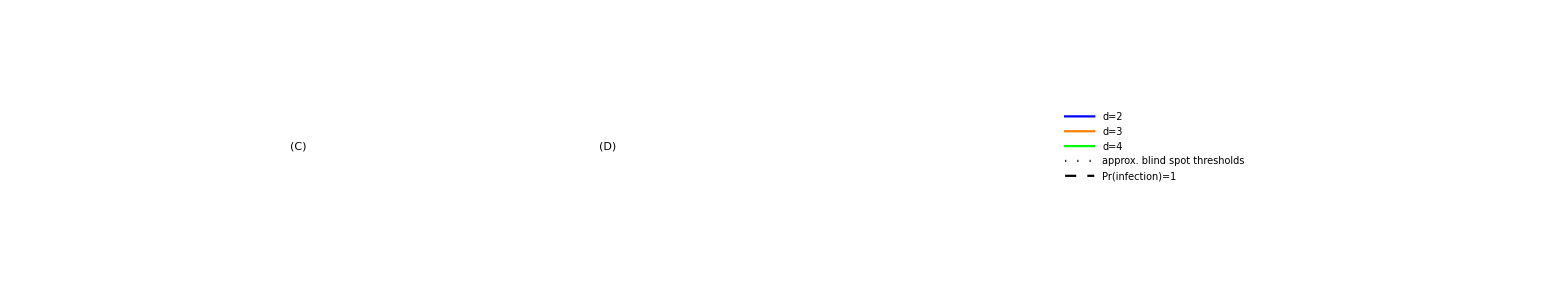

```mathematica
probplots = GraphicsRow[{everyfig, anyfig,
LineLegend[{Blue,Orange,Green,{Dotted,Black,Thick},{Dashed,Black,Thick}},{"d=2","d=3","d=4","approx. blind spot thresholds", "Pr(infection)=1"},LabelStyle->{FontSize->24}]},ImageSize->1200,
ImagePadding->{{Automatic,-500},{Automatic,Automatic}}];

IBSfig = GraphicsColumn[{bothgapplots,probplots},ImageSize->1400]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lauren/Dropbox/My Mac (Laurens-MacBook-Pro.local)/Desktop/OAS-coev-project/manuscript_submissions/revision_1/figures-public-repo-revised

```mathematica
Export["../figures/immunity_blind_spot.pdf",IBSfig]
```

../figures/immunity_blind_spot.pdf